# Analiza globalne pomoči pri zračni navigaciji (Global Air Navigation Aids)

## Pridobivanje podatkov

Naprave za pomoč pri zračni navigaciji (navigation aids oz. navaids) so radijski oddajniki, ki letalom omogočajo določanje položaja in usmerjanje med letom. Mednje spadajo naprave tipa NDB, VOR, DME, TACAN in njihove kombinacije. V nadaljevanju analiziram globalni nabor teh naprav, pridobljen iz odprtega podatkovnega vira OurAirports, ki vsebuje podatke o vrsti, frekvenci, geografski legi in državi za vsako napravo.

```mathematica
SetDirectory[NotebookDirectory[]]; 
vrsta = Import["navaids.csv", "CSV"]; 
glava = First[vrsta]; 
podatki = Rest[vrsta]; 
podatki = (PadRight[#1, Length[glava], ""] & ) /@ podatki; 
podatkiNavaids = Dataset[(AssociationThread[glava -> #1] & ) /@ podatki]
```

Dataset[<>]

Spodnja tabela povzema osnovne značilnosti podatkovnega niza. Skupno število naprav, število zajetih držav ter število različnih tipov naprav, ki jih analiziram v nadaljevanju.

```mathematica
Grid[{{"Lastnost","Podatek"},{"Vir podatkov","OurAirports (Global Navigation Aids)"},{"Število naprav",Length[data]},{"Število držav",Length[DeleteDuplicates[podatkiNavaids[All,"iso_country"]]]},{"Vrste naprav",Length[DeleteDuplicates[podatkiNavaids[All,"type"]]]}},Frame->All]
```

Lastnost | Podatek
Vir podatkov | OurAirports (Global Navigation Aids)
Število naprav | 0
Število držav | 231
Vrste naprav | 7

## Osnovni prikaz podatkov

Spodnji graf prikazuje število naprav po posameznem tipu. Iz grafa lahko razberemo, katere vrste naprav (npr. NDB, VOR-DME) so v globalnem omrežju najpogostejše.

```mathematica
BarChart[Counts[Normal[podatkiNavaids[All,"type"]]],ChartLabels->Automatic,PlotTheme->"Detailed",PlotLabel->"Število naprav po tipu",ImageSize->Large]
```

Iz grafa je razvidno, da med napravami močno prevladuje tip NDB, kar je pričakovano, saj gre za najstarejšo in najbolj razširjeno tehnologijo radijske navigacije. Sledi mu VOR-DME kot drugi najpogostejši tip, medtem ko so TACAN, VORTAC, VOR in kombinacija NDB-DME, DME v globalnem omrežju zastopani precej redkeje.

Naslednji graf prikazuje 15 držav z največjim številom nameščenih navigacijskih naprav. To nam pove, katere države imajo najgosteje razvito omrežje zračne navigacije.

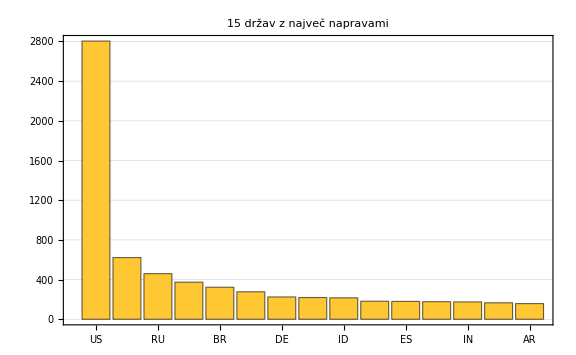

```mathematica
najDržave=TakeLargest[Counts[Normal[podatkiNavaids[All,"iso_country"]]],15];
BarChart[najDržave,ChartLabels->Keys[najDržave],PlotTheme->"Detailed",PlotLabel->"15 držav z največ napravami",ImageSize->Large]
```

Iz grafa je razvidno, da imajo ZDA daleč največje število navigacijskih naprav (skoraj 2800), kar je skladno z obsegom in gostoto ameriškega letalskega omrežja. Sledijo Kanada, Rusija in Avstralija. Geografsko velike države z razvejano letalsko infrastrukturo. Preostale države na seznamu (Brazilija, Kitajska, Nemčija, Japonska, Indonezija in druge) imajo občutno manj naprav, kar kaže, da je globalna porazdelitev zelo neenakomerna in odraža predvsem velikost ozemlja ter obseg zračnega prometa posamezne države.



Spodnji histogram prikazuje porazdelitev delovnih frekvenc naprav (v kHz). Na podlagi grafa lahko opazujemo, v katerem frekvenčnem območju deluje večina naprav.

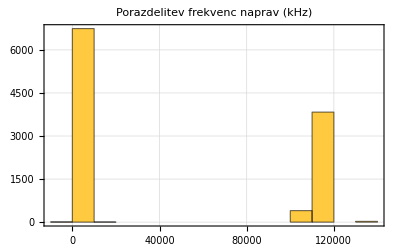

```mathematica
Histogram[podatkiNavaids[All,"frequency_khz"],PlotTheme->"Detailed",PlotLabel->"Porazdelitev frekvenc naprav (kHz)"]
```

Histogram razkriva, da se frekvence naprav jasno združujejo v dve ločeni skupini. Prva, številčnejša skupina se nahaja pri nizkih frekvencah (do približno 2000 kHz) in ustreza napravam tipa NDB, ki delujejo v dolgovalovnem/srednjevalovnem območju. Druga skupina je zgoščena okrog 108.000–118.000 kHz (tj. 108–118 MHz), kar ustreza VHF frekvencam, ki jih uporabljajo naprave tipa VOR in DME. Ta dvovrhasta porazdelitev tako neposredno odraža dve različni radijski tehnologiji, ki soobstajata v globalnem navigacijskem omrežju.

## Naprednejši prikaz rezultatov

V tem delu za vsako od 15 držav z največ napravami izračunam podrobnejšo statistiko. Skupno število naprav ter razčlenitev po posameznem tipu naprave.

```mathematica
vseDrzave=Counts[podatkiNavaids[All,"iso_country"]];


top15=TakeLargest[vseDrzave,15];


Grid[Prepend[KeyValueMap[List,top15],{"Država","Št. naprav"}],Frame->All]
```

Grid[,Frame→All]

Tabela potrjuje razmerja, ki smo jih videli na prejšnjem grafu, hkrati pa omogoča natančnejši vpogled v število naprav po posamezni državi.

Spodnji zemljevid prikazuje gostoto navigacijskih naprav po posameznih državah sveta. Temnejše obarvane države imajo večje število naprav, kar omogoča hiter geografski pregled porazdelitve infrastrukture.

```mathematica
drzaveStevilo=Counts[Normal[podatkiNavaids[All,"iso_country"]]];

pravila=KeyValueMap[Quiet@Interpreter["Country"][#1]->#2&,drzaveStevilo];

GeoRegionValuePlot[pravila,PlotLabel->"Gostota navigacijskih naprav po državah",ImageSize->Large,PlotLegends->Automatic]
```

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

General::stop: Further output of Rule::argrx will be suppressed during this calculation.

-Graphics-

Podrobnejša analiza po državah potrjuje ugotovitve iz osnovnih grafov . Največ naprav imajo geografsko velike države z razvitim letalskim prometom (ZDA, Kanada, Rusija, Avstralija), medtem ko manjše države v povprečju izkazujejo sorazmerno manjše število naprav. Razčlenitev po tipu naprave dodatno pokaže, da se sestava navigacijske infrastrukture med državami razlikuje.

## Interaktivna aplikacija

Interaktivna aplikacija uporabniku omogoča izbiro države, za katero se prikažeta število naprav in njihova geografska razporeditev na zemljevidu. Program za izbrano državo iz podatkov filtrira ustrezne naprave in jih prikaže z oznakami tipa naprave.

```mathematica
vseDrzavneKode=Normal[DeleteDuplicates[podatkiNavaids[All,"iso_country"]]];

Manipulate[With[{subset=podatkiNavaids[Select[#["iso_country"]==country&]]},Column[{Grid[{{"Država",country},{"Št. naprav",Length[subset]}},Frame->All],GeoListPlot[GeoPosition[Values[#]]&/@Normal[subset[All,{"latitude_deg","longitude_deg"}]],PlotLabel->"Naprave v državi: "<>country,ImageSize->Large]}]],{{country,"SI","Država (ISO koda)"},vseDrzavneKode}]
```